```mathematica
n = 40
y = {-2.57251482,0.33806206,2.71757796,1.09861336,2.85603752,-0.91651351,0.15555127,-2.68160347,2.47043789,3.47459025,1.63949862,-1.32148757,2.64187513,0.30357848,-4.09546231,-1.50709863,-0.99517866,-2.0648892,-2.40317949,3.46383544,0.91173696,1.18222221,0.04235722,-0.52815171,1.15551598,-1.62749724,0.71473237,-1.08458812,4.66020296,1.24563831,-0.67970862,0.93461681,1.18187607,-1.49501051,2.44755622,-2.06424237,-0.04584074,1.93396696,1.07685273,-0.09837907}
```

```mathematica
epslist = Table[eps,{eps,-1,1,0.5}]
```

{-1.,-0.5,0.,0.5,1.}

```mathematica
pmu1[mu1_,eps_]:=1/(20 - eps)*Boole[-10+eps<= mu1 && mu1 <= 10]
```

```mathematica
pmu2[mu2_]:=1/20*Boole[-10<= mu2 && mu2 <= 10]
```

```mathematica
pu[mu1_, mu2_, eps_]:=pmu1[mu1, eps] * pmu2[mu2]
```

```mathematica
L[mu1_, mu2_, y_]:= PDF[NormalDistribution[mu1+mu2,1],y]
```

```mathematica
For[i=1, i<=n,i++, 
pu[mu1_, mu2_, eps_]=pu[mu1, mu2, eps] * L[mu1, mu2, y[[i]]];
Print[L[0, 0, y[[i]]]]
]
```

0.0145836

0.376785

0.00993637

0.218185

0.0067554

0.262124

0.394145

0.0109498

0.0188646

0.000953542

0.104047

0.166609

0.0121711

0.380976

0.0000909369

0.128143

0.243137

0.04732

0.0222242

0.000989791

0.263271

0.198342

0.398585

0.347007

0.204631

0.106106

0.309017

0.221551

7.67391×10^-6

0.183646

0.316656

0.257769

0.198423

0.130489

0.0199564

0.0473832

0.398523

0.0614794

0.22341

0.397016

```mathematica
Simplify[pu[mu1,mu2,eps]]
```

-1/(-20.+eps)1.27547×10^-51 ⅇ^(-20. mu1^2+mu1 (12.4656-40. mu2)+(12.4656-20. mu2) mu2) Boole[eps≤10+mu1&&mu1≤10] Boole[-10≤mu2≤10]

```mathematica
{t, n} = Timing[NIntegrate[pu[mu1, mu2,eps=0],  {mu1,-∞, ∞}, {mu2,-∞, ∞}, AccuracyGoal->55]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{3.78801,2.80951×10^-51}

```mathematica
{t, pmu1margin[mu1_]}= Timing[ Integrate[pu[mu1,mu2]/n, {mu2, -∞, ∞}]]
```

{4.55564,Piecewise[{{0.0313766 (Erf[46.1151-4.47214 mu1]+Erf[43.3277+4.47214 mu1]), -10.≤mu1≤10.}, {0., True}}]}

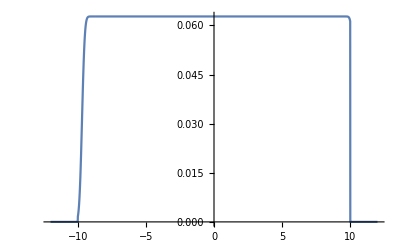

```mathematica
Plot[pmu1margin[mu1],{mu1,-12,12},PlotRange->Full]
```

```mathematica
postlist = Table[x, Length[epslist]]
```

{x,x,x,x,x}

```mathematica
For[i=1, i <= Length[epslist], i++,
n = Integrate[pu[mu1, mu2,eps=epslist[[i]]],  {mu1,-∞, ∞}, {mu2,-∞, ∞}];
Print[n];
pmu1margin[mu1_]= Integrate[pu[mu1,mu2,eps=epslist[[i]]]/n, {mu2, -∞, ∞}];
postlist[[i]] = pmu1margin[mu1];
]
```

3.30563×10^-51

3.38626×10^-51

3.47066×10^-51

3.52422×10^-51

3.52585×10^-51

```mathematica
Integrate[postlist[[1]], {mu1, -15,15}]
```

1.

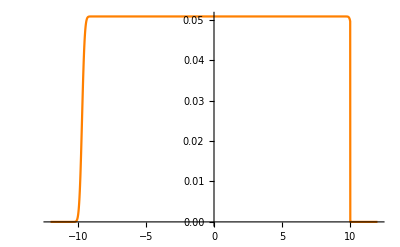

```mathematica
Plot[postlist[[1]],{mu1,-12,12},PlotStyle->Orange]
```

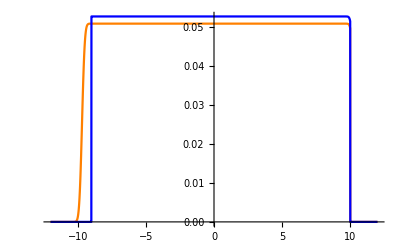

```mathematica
Show[{Plot[postlist[[1]],{mu1,-12,12},PlotStyle->Orange],Plot[postlist[[5]],{mu1,-12,12},PlotStyle->Blue]},PlotRange->All,AxesOrigin->{0,0}]
```